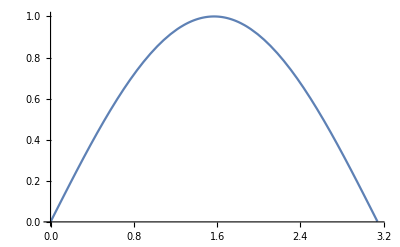

```mathematica
Plot[Sin[x],{x,0,3.14}]
```

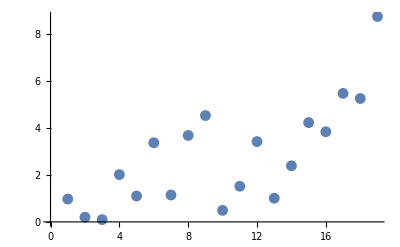

```mathematica
ListPlot[Table[RandomReal[x],{x,1,10,0.5}]]
```

```mathematica
ListLinePlot[Table[RandomReal[x],{x,1,10,0.5}]]
```

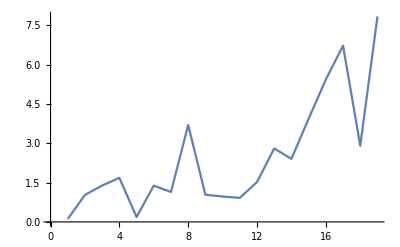

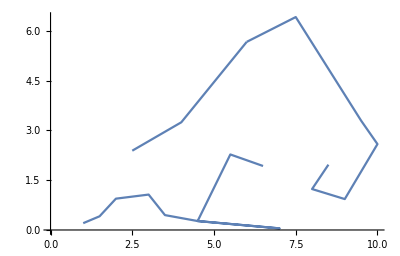

```mathematica
ListCurvePathPlot[Table[{x,RandomReal[x]},{x,1,10,0.5}]]
```

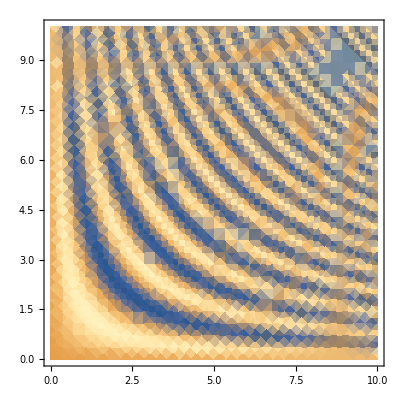

```mathematica
DensityPlot[Sin[x*y],{x,0,10},{y,0,10}]
```

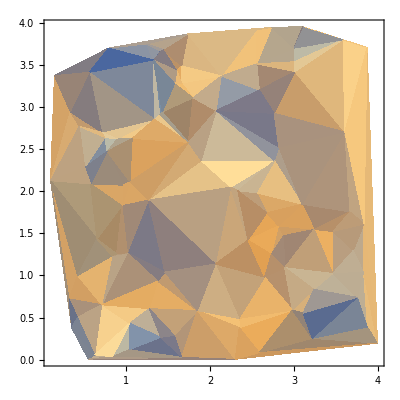

```mathematica
ListDensityPlot[RandomReal[{0,4},{100,3}]]
```

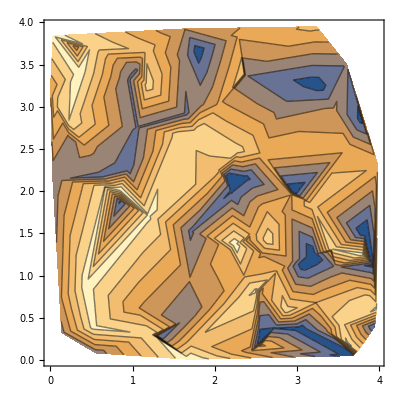

```mathematica
ListContourPlot[RandomReal[{0,4},{100,3}]]
```

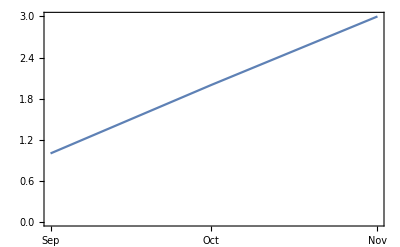

```mathematica
DateListPlot[{1,2,3},{2008,9}]
```

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/3},{t,0,15}]
```

-Graphics3D-

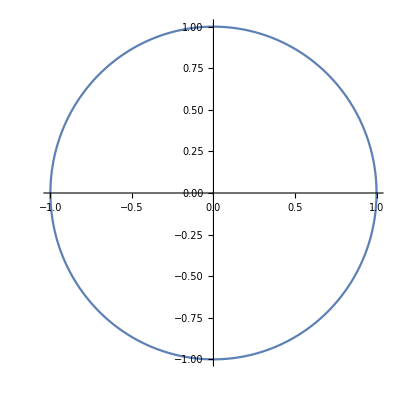

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]
```

```mathematica
Needs["StatisticalPlots`"]
```

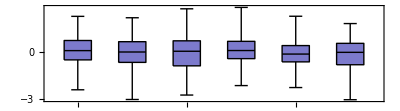

```mathematica
BoxWhiskerPlot[RandomReal[NormalDistribution[0,1],{100,6}]]
```

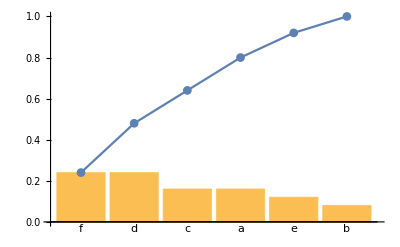

```mathematica
data=RandomChoice[CharacterRange["a","f"],{25}];
ParetoPlot[data]
```

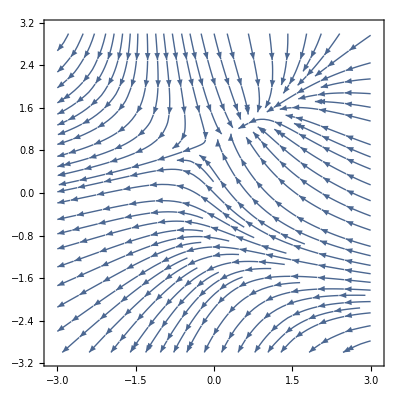

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
StreamPlot[{{x,y},{y,-x}},{x,-3,3},{y,-3,3}]
```

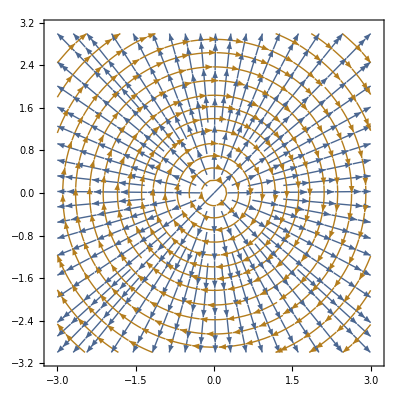

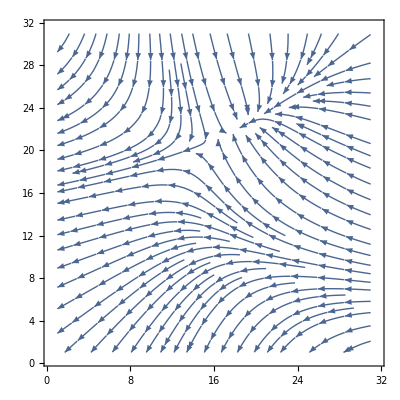

```mathematica
data=Table[{-1-x^2+y,1+x-y^2},{x,-3,3,.2},{y,-3,3,.2}];
ListStreamPlot[data]
```

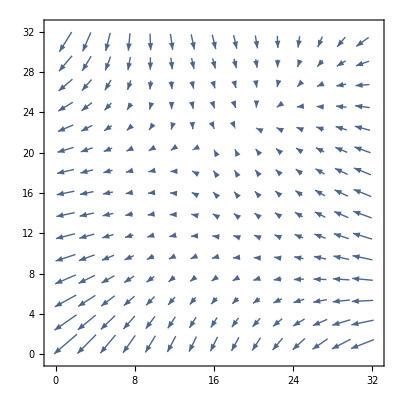

```mathematica
ListVectorPlot[data]
```

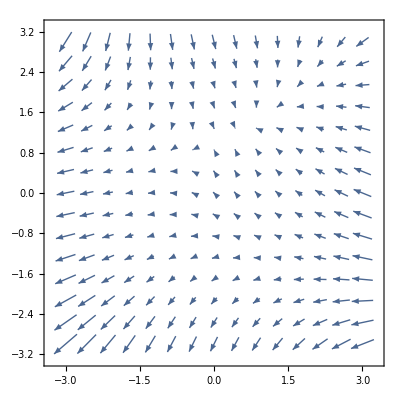

```mathematica
VectorPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
PieChart[{1,2,3,4,5}]
```

-Graphics-

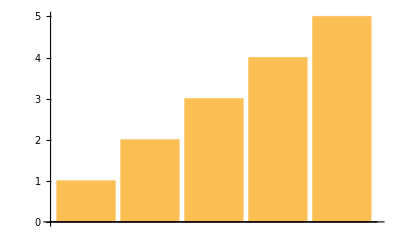

```mathematica
BarChart[{1,2,3,4,5}]
```

```mathematica
PieChart3D[{1,23,4,352,2,42}]
```

-Graphics3D-

```mathematica
BarChart3D[{1,124,2,2,2,1,1,2,42,4}]
```

-Graphics3D-

```mathematica
SectorChart[{{{1,1},{1,2},{1,3}},{{7,3},{5,2},{1,1}}}]
```

-Graphics-

```mathematica
GeoGraphics[GeoRange->"World",GeoProjection->"Robinson"]
```

-Graphics-

```mathematica
s=GeoGraphics[{GeoPosition[{{34,112},{45,123}}],GeoPosition[{{48,112},{53,123}}]},Axes->True]
```

-Graphics-

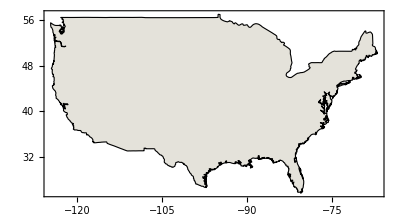

```mathematica
Show[CountryData["UnitedStates",{"Shape","Mercator"}],Frame->True]
```

```mathematica
GeoRegionValuePlot[{LinguisticAssistant->2,LinguisticAssistant->3,LinguisticAssistant->4,LinguisticAssistant->5,LinguisticAssistant->6,LinguisticAssistant->7}]
```

-Graphics-

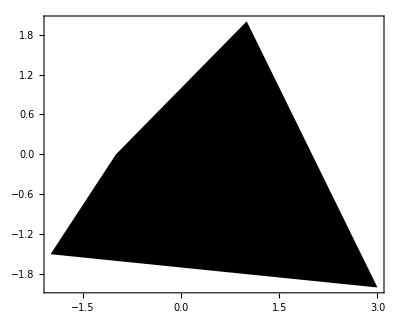

```mathematica
Graphics[Polygon[{{-1,0},{1,2},{3,-2},{-2,-1.5}}],Frame->True]
```

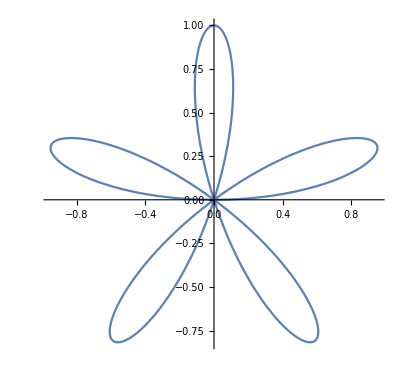

```mathematica
PolarPlot[Sin[5θ],{θ,0,π}]
```

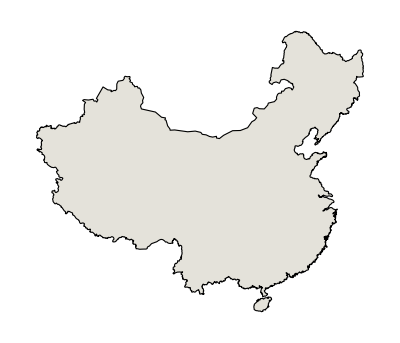

```mathematica
CountryData[LinguisticAssistant,"Shape"]
```

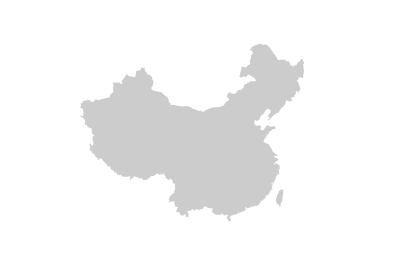

```mathematica
GeoGraphics[Polygon[{LinguisticAssistant,LinguisticAssistant}],GeoBackground->None]
```

```mathematica
x=Table[GeoPosition[{RandomReal[{-90,90}],RandomReal[{-180,180}]}],{i,200}];
GeoListPlot[x]
```

-Graphics-

```mathematica
GeoGraphics[Point[x]]
```

-Graphics-

```mathematica
data=DeleteCases[Reverse[CityData[#,"Coordinates"]]&/@CityData[{All,"India"}],Missing["NotAvailable"]];
Show[SmoothDensityHistogram[data,.3,ColorFunction->"SunsetColors",PlotPoints->150,Mesh->20,MeshStyle->Opacity[.1],PlotRange->All],Graphics[{FaceForm[],EdgeForm[Directive[White,Opacity[.7]]],CountryData["India","Polygon"]}]]
```

-Graphics-

```mathematica
outlines=Table[DeleteCases[CountryData[r,"SchematicPolygon"],Polygon[_Missing]],{r,{"SouthAmerica","NorthAmerica","Africa","Europe","Asia","Australia"}}]
```

{1}
 |  |  |  |

```mathematica
ListDensityPlot[Reverse@data,ColorFunction->"DeepSeaColors",AspectRatio->Automatic,DataRange->{{-180,180},{-90,90}},Epilog->{FaceForm[],EdgeForm[Opacity[0.5]],outlines},PlotRange->{{-180,180},{-90,90}}]
```

-Graphics-

```mathematica
outlines
```

{1}
 |  |  |  |

```mathematica
Graphics[{FaceForm[],EdgeForm[Black],outlines},Frame->True]
```

-Graphics-

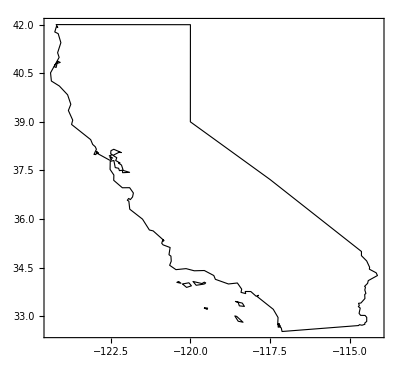

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],LinguisticAssistant["Polygon"]},Frame->True]
```

```mathematica
x=LinguisticAssistant["Polygon"];
```

```mathematica
Polygon[LinguisticAssistant]
```

Polygon[Entity[AdministrativeDivision,{California,UnitedStates}]]

```mathematica
xkcdStyle = {FontFamily -> "Comic Sans MS", 16};

xkcdLabel[{str_, {x1_, y1_}, {xo_, yo_}}] := Module[{x2, y2},
   x2 = x1 + xo; y2 = y1 + yo;
   {Inset[
     Style[str, xkcdStyle], {x2, y2}, {1.2 Sign[x1 - x2], 
      Sign[y1 - y2] Boole[x1 == x2]}], Thick, 
    BezierCurve[{{0.9 x1 + 0.1 x2, 0.9 y1 + 0.1 y2}, {x1, y2}, {x2, y2}}]}];

xkcdRules = {EdgeForm[ef:Except[None]] :> EdgeForm[Flatten@{ef, Thick, Black}], 
   Style[x_, st_] :> Style[x, xkcdStyle], 
   Pane[s_String] :> Pane[Style[s, xkcdStyle]],
   {h_Hue, l_Line} :> {Thickness[0.02], White, l, Thick, h, l},
   Grid[{{g_Graphics, s_String}}] :> Grid[{{g, Style[s, xkcdStyle]}}],
   Rule[PlotLabel, lab_] :> Rule[PlotLabel, Style[lab, xkcdStyle]]};

xkcdShow[p_] := Show[p, AxesStyle -> Thick, LabelStyle -> xkcdStyle] /. xkcdRules

xkcdShow[Labeled[p_, rest__]] := 
 Labeled[Show[p, AxesStyle -> Thick, LabelStyle -> xkcdStyle], rest] /. xkcdRules

xkcdDistort[p_] := Module[{r, ix, iy},
   r = ImagePad[Rasterize@p, 10, Padding -> White];
   {ix, iy} = 
    Table[RandomImage[{-1, 1}, ImageDimensions@r]~ImageConvolve~
      GaussianMatrix[10], {2}];
   ImagePad[ImageTransformation[r, 
     # + 15 {ImageValue[ix, #], ImageValue[iy, #]} &, DataRange -> Full], -5]];

xkcdConvert[x_] := xkcdDistort[xkcdShow[x]]
```

```mathematica
f1[x_] := 5 + 50 (1 + Erf[x - 5]);
f2[x_] := 20 + 30 (1 - Erf[x - 5]);
xkcdConvert[Plot[{f1[x], f2[x]}, {x, 0, 10},
  Epilog -> 
   xkcdLabel /@ {{"Label 1", {1, f1[1]}, {1, 30}}, {"Label 2", {8, f2[8]}, {0, 30}}},
  Ticks -> {{{3.5, "1st Event"}, {7, "2nd Event"}}, Automatic}]]
```

$Aborted

```mathematica
temperature=Table[{x,y,AirTemperatureData[{y,x},DateObject[{2013,6,27},TimeObject[{11}]]]},{x,166,178.5,0.5},{y,-47,-34,0.5}]//Select[Flatten[#,1],FreeQ[#,"NotAvailable"]&]&;
plot=ListDensityPlot[temperature,ColorFunction->"TemperatureMap",AspectRatio->1,Frame->False,PlotRange->All];
GeoGraphics[{GeoStyling[{"GeoImage",plot}],EdgeForm[Thin],Polygon[Entity["Country","NewZealand"]]},GeoRange->{{-47,-34},{162,182.5}}]
```

-Graphics-

```mathematica
data={#["Position"],#["Depth"]}&/@Values[EarthquakeData[Rectangle[{128,30},{147,46}],5,{{2000,1,1},{2010,1,1}}]];
```

```mathematica
Graphics3D[{Opacity[0.6],RGBColor[.6,.73,.36],Map[Append[Reverse[#],0]&,Entity["Country","Japan"]["Polygon"]/.GeoPosition->Identity,{-2}],RGBColor[.49,0,0],Opacity[0.6],Line[{Append[Reverse[First[#1]],0],Append[Reverse[First[#1]],-QuantityMagnitude[#2]/10]}&@@@data]},Axes->True,BoxRatios->{1,1,1/2}]
```

-Graphics3D-

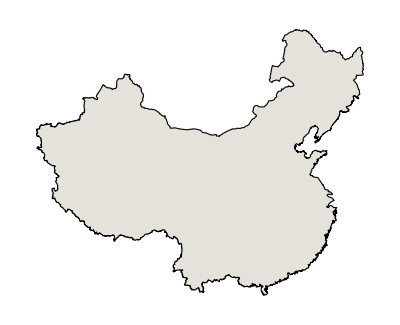

```mathematica
Graphics[CountryData["China","Shape"]]
```